```mathematica
Roots[-λ^3 + 2*d*λ^2 + (u^2 + a^2)*λ - 2*d*a^2==0,λ]
```

λ==(2 d)/3+(2^(1/3) (-4 d^2-3 (a^2+u^2)))/(3 (36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))-((36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))/(3 2^(1/3))||λ==(2 d)/3-((1+ⅈ √3) (-4 d^2-3 (a^2+u^2)))/(3 2^(2/3) (36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))+((1-ⅈ √3) (36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))/(6 2^(1/3))||λ==(2 d)/3-((1-ⅈ √3) (-4 d^2-3 (a^2+u^2)))/(3 2^(2/3) (36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))+((1+ⅈ √3) (36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))/(6 2^(1/3))

```mathematica
Λ[d_,a_,u_]:= (2 d)/3-((1-ⅈ √3) (-4 d^2-3 (a^2+u^2)))/(3 2^(2/3) (36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))+((1+ⅈ √3) (36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))/(6 2^(1/3))

Λminus[d_,a_,u_]:=(2 d)/3+(2^(1/3) (-4 d^2-3 (a^2+u^2)))/(3 (36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))-((36 a^2 d-16 d^3-18 d u^2+√((36 a^2 d-16 d^3-18 d u^2)^2+4 (-4 d^2-3 (a^2+u^2))^3))^(1/3))/(3 2^(1/3))

Λapprox[d_,a_,u_]:= 2*d/3*(1+(2*a^2/u^2 - 1)/(a^2/u^2 + 1))
Λtest[d_,a_,u_]:= (2d)/3+((1-ⅈ √3) (3^2*(d/u)*(2*a^2/u^2-1)-ⅈ*Sqrt[3]*3*(1+a^2/u^2)^(3/2))^(1/3)*u)/6+((1+ⅈ √3) (3^2*(d/u)*(2*a^2/u^2-1)+ⅈ*Sqrt[3]*3*(1+a^2/u^2)^(3/2))^(1/3)*u)/6
```

```mathematica
Limit[D[ArcTan[α/y],{y,1}],y->0]
Limit[D[ArcTan[α/y],{y,2}],y->0]
Limit[D[ArcTan[α/y],{y,3}],y->0]
D[ArcTan[α/y],{y,2}]
D[ArcTan[α/y],{y,3}]
```

-1/α

0

2/α^3

-(2 α^3)/(y^5 (1+α^2/y^2)^2)+(2 α)/(y^3 (1+α^2/y^2))

-(8 α^5)/(y^8 (1+α^2/y^2)^3)+(14 α^3)/(y^6 (1+α^2/y^2)^2)-(6 α)/(y^4 (1+α^2/y^2))

1

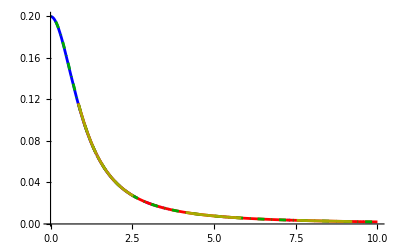

```mathematica
a0 = 1
Show[Plot[Λ[0.1,a0,u],{u,0,10}, PlotRange-> All, PlotStyle-> Blue],Plot[Λtest[0.1,a0,u],{u,0,10}, PlotStyle->Red],Plot[Λapprox[0.1,a0,u],{u,0,10}, PlotStyle->{Darker[Green], DotDashed}, PlotRange-> {-2,0.2}],Plot[Λtest2[0.1,a0,u],{u,0,10}, PlotStyle->{Darker[Yellow], Dashing[0.1]}]]
```

```mathematica
Λ[0.1,0,1]
Λtest[0.1,0,1]
Λapprox[0.1,0,1]
```

-1.249×10^-16-2.22045×10^-16 ⅈ

0.000365039+0. ⅈ

0.

```mathematica
θ2[d_,a_,u_]:=Piecewise[{{ArcTan[Sqrt[3]*(1+a^2/u^2)^(3/2)/(3*(d/u)*(2*a^2/u^2-1))],a^2/u^2>1},{(ArcTan[Sqrt[3]*(1+a^2/u^2)^(3/2)/(3*(d/u)*(2*a^2/u^2-1))]+Pi),a^2/u^2<1}}]
θ2approx[d_,a_,u_]:=Pi/2- (Sqrt[3]*(1+a^2/u^2)^(3/2)/(3*(2*a^2/u^2-1)))^(-1)*(d/u)
```

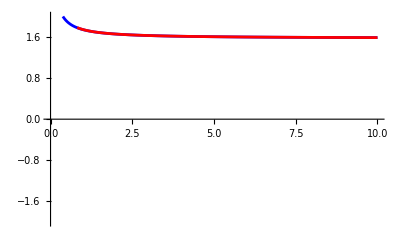

```mathematica
Show[Plot[θ2[0.1,0,u],{u,0,10}, PlotRange-> {-2,2}, PlotStyle-> Blue],Plot[θ2approx[0.1,0,u],{u,0,10}, PlotStyle->Red]]
```

```mathematica
z[d_,a_,u_] := 9*(d/u)*(2*a^2/u^2-1) + ⅈ*3*Sqrt[3]*(1+a^2/u^2)^(3/2)
ztest[d_,a_,u_]:= Sqrt[3]*3*(1+a^2/u^2)^(3/2)*Exp[ⅈ*θ2approx[d,a,u]]
```

```mathematica
2*0.1/3 + ((1+Sqrt[3]*ⅈ)*z[0.1,0.5,1]^(1/3) + (1-Sqrt[3]*ⅈ)*Conjugate[z[0.1,0.5,1]]^(1/3) )*1/6
2*0.1/3 +( (1+Sqrt[3]*ⅈ)*ztest[0.1,0.5,1]^(1/3) + (1-Sqrt[3]*ⅈ)*Conjugate[ztest[0.1,0.5,1]]^(1/3))*1/6
2*0.1/3 + 2*ρ1*ρ2approx[0.1,0.5,1]^(1/3)*1/(3*ξ[0.1,0.5,1])*(0.1/1)*(1/6)
4*0.1*(0.5^2/1^2 - 1/3)
```

0.0400189+0. ⅈ

0.0400019+0. ⅈ

0.04

-0.0333333

```mathematica
ρ2approx[d_,a_,u_]:= Sqrt[3]*3*(1+a^2/u^2)^(3/2)
```

```mathematica
ρ1 = 2
θ1 = Pi/3
w2test[d_,a_,u_]:=2*ρ1*ρ2approx[d,a,u]^(1/3)*Cos[θ1 + θ2approx[d,a,u]/3 ]
```

2

π/3

```mathematica
ξ[d_,a_,u_]:=Sqrt[3]*(1+a^2/u^2)^(3/2)/(3*(2*a^2/u^2 -1))
```

```mathematica
2*0.1/3 +( (1+Sqrt[3]*ⅈ)*ztest[0.1,0.5,1]^(1/3) + (1-Sqrt[3]*ⅈ)*Conjugate[ztest[0.1,0.5,1]]^(1/3))*1/6
2*0.1/3 +2*ρ1*ρ2approx[0.1,0.5,1]^(1/3)*Cos[θ1 + θ2approx[0.1,0.5,1]/3 ]*1/6
2*0.1/3 +2*ρ1*ρ2approx[0.1,0.5,1]^(1/3)*(1/3)*(1/ξ[0.1,0.5,1])*(0.1/1)*1/6
```

0.0400019+0. ⅈ

0.0400019

0.064

```mathematica
2*ρ1*
```

```mathematica
Λtest2[d_,a_,u_]:= 2*d/3 + (1-ⅈ*Sqrt[3])*u*(Conjugate[ztest[d,a,u]])^(1/3)/6+ (1+ⅈ*Sqrt[3])*u*(ztest[d,a,u])^(1/3)/6
```

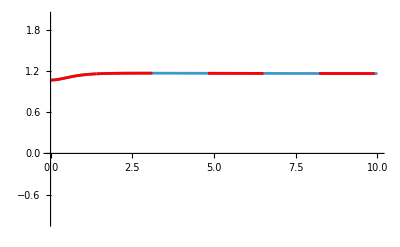

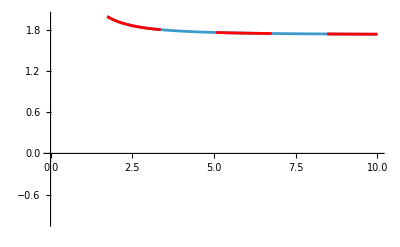

```mathematica
Show[Plot[Arg[z[0.1,1,u]]^(1/3),{u,0,10}, PlotRange-> {-1,2}],Plot[Arg[ztest[0.1,1,u]]^(1/3),{u,0,10}, PlotRange-> {-1,2}, PlotStyle->{Red, Dashing[0.1]}]]
Show[Plot[Abs[z[0.1,1,u]]^(1/3),{u,0,10}, PlotRange-> {-1,2}],Plot[Abs[ztest[0.1,1,u]]^(1/3),{u,0,10}, PlotRange-> {-1,2}, PlotStyle->{Red, Dashing[0.1]}]]
```

```mathematica
Abs[(1+Sqrt[3]*ⅈ)]
Arg[(1+Sqrt[3]*ⅈ)]
```

2

π/3

```mathematica
Cos[2*Pi/3]
Sin[2*Pi/3]
```

-1/2

(√3)/2

```mathematica
Cos[4*Pi/3]
Sin[4*Pi/3]
```

-1/2

-(√3)/2

```mathematica
f[λ_,d_,a_,u_]:= -λ^3 + 2*d*λ^2 + (u^2 + a^2)*λ - 2*d*a^2
```

0.1

1

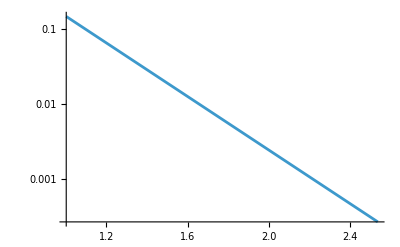

```mathematica
d=0.1
a = 1
LogPlot[f[Sqrt[3]*d*a^2/u^2,d,a,u],{u,1,100000}, PlotRange->All]
```

```mathematica
Limit[f[1*d*a^2/u^2,d,a,u],u-> Infinity]
```

-0.1

```mathematica
d = 0.1
a = 0
f[4*d*a^2/u^2,d,a,u]
```

0.1

0

0.

```mathematica
Exp[ⅈ*θ1]*Exp[ⅈ*θ2[0.1,0.5,1]/3]+Exp[-ⅈ*θ1]*Exp[-ⅈ*θ2[0.1,0.5,1]/3]
2*Cos[θ1+θ2[0.1,0.5,1]/3 ]
```

-0.0412561+0. ⅈ

-0.0412561

```mathematica
Cos[θ1+θ2[0.1,0.5,1]/3 ]
(1/3)*(1/ξ[0.1,0.5,1])*(0.1/1)
```

-0.0206281

-0.00206559

```mathematica
θ2[0.1,0.5,1]/3
```

0.544228

```mathematica
0.1/10
ξ[0.1,0.5,10]
1/(3*ξ[0.1,0.5,10])*(0.1/10)
```

0.01

-0.582429

-0.00572316

```mathematica
Cos[Pi/2]
```

0

```mathematica
Cos[θ1+θ2[0.1,0.5,1]/3]
Cos[θ1+θ2approx[0.1,0.5,1]/3] 
Cos[Pi/2 -1/(3*ξ[0.1,0.5,1])*(0.1/1)]
1/(3*ξ[0.1,0.5,1])*(0.1/1)
(*CARREGAR MAIS UM TERMO NA EXPANSÃO*)
```

-0.0206281

-0.0206544

-0.0206544

-0.0206559

```mathematica
2*Cos[θ1+θ2[0.1,0.5,1]/3]
2*Cos[θ1+θ2approx[0.1,0.5,1]/3] 
2*Cos[Pi/2 -1/(3*ξ[0.1,0.5,1])*(0.1/1)]
2*1/(3*ξ[0.1,0.5,1])*(0.1/1)
```

-0.0412561

-0.0413089

-0.0413089

-0.0413118

```mathematica
Pi/6- θ2[0.1,0.5,1]/3
```

-0.0206295

```mathematica
Pi/2 + 1/(3*ξ[0.1,0.5,10])*(0.1/10)
```

```mathematica
Pi/3+Pi/6
```

π/2

```mathematica
θ1+θ2[0.1,0.5,1]/3
θ1+θ2approx[0.1,0.5,1]/3 
Pi/2 -1/( 3*ξ[0.1,0.5,1])*(0.1/1)
Pi/2 -1/( 3*ξ[0.1,0.5,1])*(0.1/1) + 2/( 3*ξ[0.1,0.5,1]^3)*(0.1/1)^3
```

1.59143

1.59145

1.59145

1.59129

```mathematica
1/(3* ξ[0.1,0.5,10])*(0.1/10)
```

-0.00572316

```mathematica
Series[ArcTan[α/x],x==β]
```

Power::infy: Infinite expression 1/0 encountered.

Series::sspec: 0==β is not a valid expansion point specification.

Series[Indeterminate,0==β]

```mathematica
2*0.1/3 + 2*ρ1*ρ2approx[0.1,0.5,1]*1/(3*ξ[0.1,0.5,1])*(0.1/1)*1/6
```

-0.0333333

```mathematica
2*0.1/3
```

0.0666667

```mathematica
Λ[0.1,0.5,1]
```

0.039797+1.11022×10^-16 ⅈ

100

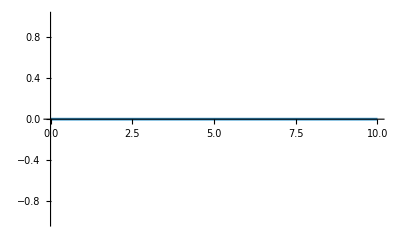

```mathematica
d = 100
Plot[f[Λapprox[d,a,u],d,a,u],{u,0,10}]
```

```mathematica
1==1
```

True

```mathematica
x^2 == (x^2 + x-x)
```

True

```mathematica
N[Λ[d,a,1]]==Λapprox[d,a,1]
```

False

```mathematica
N[Λ[d,a,1]]==Λapprox[d,a,1]
```

False

```mathematica
N[Λ[d,a,1]]
```

5.68434×10^-14-2.13163×10^-14 ⅈ

## Minimal time-averaged excess work

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[Sqrt[1+y'[x]^2],y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))==0

```mathematica
dΩp[t_]:=D[Ωp[b],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_]:=2*(dΩp[t]*Ωs[t]-Ωp[t]*dΩs[t])/(Ωp[t]^2 + Ωs[t]^2) 
Ω[t_]:= Sqrt[Ωp[t]^2  + Ωs[t]^2]
```

```mathematica
F[t_] :=Ωa[t]^2/(Ωa[t]^2 + Ω[t]^2)
```

```mathematica
Ωs[t_]:= 1
Simplify[EulerEquations[F[t],Ωp[t],t]]
```

((1+Ωp[t]^2) (1+3 Ωp[t]^2+3 Ωp[t]^4+Ωp[t]^6-12 Ωp'[t]^2) (-3 Ωp[t] Ωp'[t]^2+Ωp''[t]+Ωp[t]^2 Ωp''[t]))/(1+3 Ωp[t]^2+3 Ωp[t]^4+Ωp[t]^6+4 Ωp'[t]^2)==0

```mathematica
Ωa[t]
```

(2 Ωp'[t])/(1+Ωp[t]^2)

```mathematica
Sol=NDSolve[{(1+Ωp[t]^2) (1+3 Ωp[t]^2+3 Ωp[t]^4+Ωp[t]^6-12 Ωp'[t]^2) (-3 Ωp[t] Ωp'[t]^2+Ωp''[t]+Ωp[t]^2 Ωp''[t])==0, Ωp[0]==0.1, Ωp[1]==10},Ωp[t],{t,0,1}]
```

{{Ωp[t]→InterpolatingFunction[…][t]}}

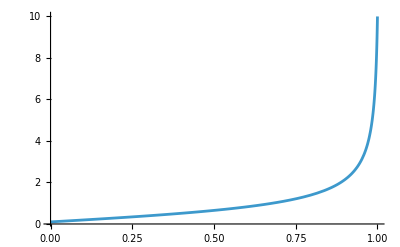

```mathematica
Plot[Evaluate[Ωp[t]/.Sol],{t,0,1}, PlotRange->All]
```

## Minimal Santos & Sarandy energetic cost

```mathematica
Needs["VariationalMethods`"]
Δ = 0.1
Ωs[t_]:=1
dΩp[t_]:=D[Ωp[b],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_]:=2*(dΩp[t]*Ωs[t]-Ωp[t]*dΩs[t])/(Ωp[t]^2 + Ωs[t]^2) 
Ω[t_]:= Sqrt[Ωp[t]^2  + Ωs[t]^2]
F2[t_] :=Ωp[t]^2 + Ωs[t]^2 + Ωa[t]^2 + 2*Δ^2
F3[t_] :=Ωa[t]^2
```

0.1

```mathematica
Sol2=NDSolve[{(-4.08 Ωp''[t]+Ωp[t] (1.02+16.16 Ωp'[t]^2+Ωp[t] (-16.240000000000002 Ωp''[t]+Ωp[t] (6.1+48.32 Ωp'[t]^2+Ωp[t] (-24.240000000000002 Ωp''[t]+Ωp[t] (15.200000000000001+48.16 Ωp'[t]^2+Ωp[t] (-16.08 Ωp''[t]+Ωp[t] (20.2+15.100000000000001 Ωp[t]^2+6.02 Ωp[t]^4+Ωp[t]^6+16. Ωp'[t]^2-4. Ωp[t] Ωp''[t]))))))))==0, Ωp[0]==0.1, Ωp[1]==10},Ωp[t],{t,0,1}]
```

NDSolve::ndsz: At t == 0.0741424, step size is effectively zero; singularity or stiff system suspected.

NDSolve[{-4.08 Ωp''[t]+Ωp[t] (1.02+16.16 Ωp'[t]^2+Ωp[t] (-16.24 Ωp''[t]+Ωp[t] (6.1+48.32 Ωp'[t]^2+Ωp[t] (-24.24 Ωp''[t]+Ωp[t] (15.2+48.16 Ωp'[t]^2+Ωp[t] (-16.08 Ωp''[t]+Ωp[t] (20.2+15.1 Ωp[t]^2+6.02 Ωp[t]^4+Ωp[t]^6+16. Ωp'[t]^2-4. Ωp[t] Ωp''[t])))))))==0,Ωp[0]==0.1,Ωp[1]==10},Ωp[t],{t,0,1}]

```mathematica
Sol3=NDSolve[{Ωp''[t]==(2 Ωp[t] Ωp'[t]^2)/(1+Ωp[t]^2), Ωp[0]==0.1, Ωp[1]==10},Ωp[t],{t,0,1}]
```

{{Ωp[t]→InterpolatingFunction[…][t]}}

```mathematica
FullSimplify[EulerEquations[F3[t],Ωp[t],t]]
```

Ωp''[t]==(2 Ωp[t] Ωp'[t]^2)/(1+Ωp[t]^2)

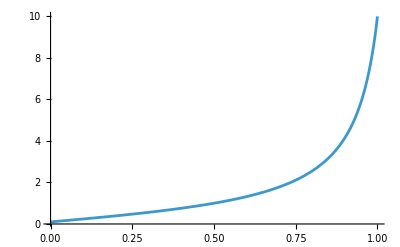

```mathematica
Plot[Evaluate[Ωp[t]/.Sol3],{t,0,1}, PlotRange->All]
```

```mathematica
FullSimplify[EulerEquations[F2[t],Ωp[t],t]]/.Ωp[t]->Ωp[t]/Sqrt[1+Ωp[t]^2/Ωmax^2]
```

(Ωp[t] ((1+Ωp[t]^2/(1+Ωp[t]^2/Ωmax^2))^3+8 Ωp'[t]^2))/(√(1+Ωp[t]^2/Ωmax^2) (1+Ωp[t]^2/(1+Ωp[t]^2/Ωmax^2)))==4 Ωp''[t]

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
Sol2=NDSolve[{EulerEquations[F2[t],Ωp[t],t], Ωp[0]==0.1, Ωp[1]==10},Ωp[t],{t,0,1}]
```

NDSolve::ndsz: At t == 0.151181, step size is effectively zero; singularity or stiff system suspected.

NDSolve[{2 (Ωp[t]+(8 Ωp[t] Ωp'[t]^2)/((1+Ωp[t]^2)^3)-(4 Ωp''[t])/((1+Ωp[t]^2)^2))==0,Ωp[0]==0.1,Ωp[1]==10},Ωp[t],{t,0,1}]

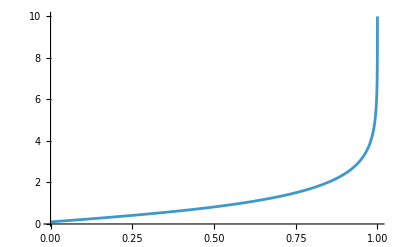

```mathematica
Plot[Evaluate[Ωp[t]/.Solteste],{t,0,1}, PlotRange->All]
```

```mathematica
4^7
```

16384

```mathematica
(Ωp[t] ((1+Ωp[t]^2/(1+Ωp[t]^2/Ωmax^2))^3+8 Ωp'[t]^2))/(√(1+Ωp[t]^2/Ωmax^2) (1+Ωp[t]^2/(1+Ωp[t]^2/Ωmax^2)))==4 Ωp''[t]
```

```mathematica
Ωmax=1.55
Solteste=NDSolve[{(Ωp[t] ((1+Ωp[t]^2/(1+Ωp[t]^2/Ωmax^2))^3+8 (Ωp'[t])^2))/(√(1+Ωp[t]^2/Ωmax^2) (1+Ωp[t]^2/(1+Ωp[t]^2/Ωmax^2)))==4*Ωp''[t], Ωp[0]==0.1, Ωp[1]==10},Ωp[t],{t,0,1}]
```

1.55

{{Ωp[t]→InterpolatingFunction[…][t]}}

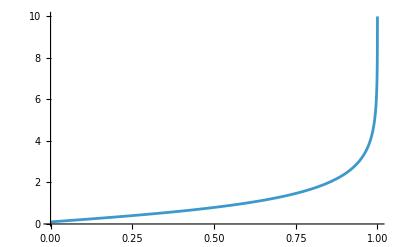

```mathematica
Plot[Evaluate[Ωp[t]/.Solteste],{t,0,1}, PlotRange->All]
```

```mathematica
D[(Ωp[t]/Sqrt[1+Ωp[t]^2/Ωmax^2]),{t,2}]
```

-(Ωp[t] Ωp'[t]^2)/(50 (1+Ωp[t]^2/100)^(3/2))+Ωp''[t]/(√(1+Ωp[t]^2/100))+Ωp[t] ((3 Ωp[t]^2 Ωp'[t]^2)/(10000 (1+Ωp[t]^2/100)^(5/2))-Ωp'[t]^2/(100 (1+Ωp[t]^2/100)^(3/2))-(Ωp[t] Ωp''[t])/(100 (1+Ωp[t]^2/100)^(3/2)))

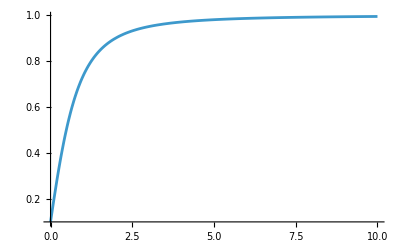

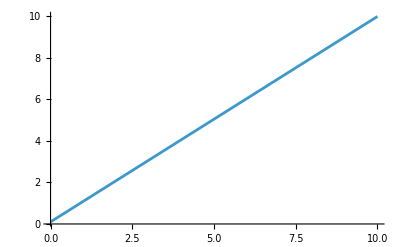

```mathematica
Plot[Ωp[t,10]/Sqrt[1+Ωp[t,10]^2/Ωmax^2],{t,0,10}, PlotRange->All]
Plot[Ωp[t,10],{t,0,10}, PlotRange->All]
```